```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
threshold = 1;
case=3;
Switch[case,
1,T=100;C0=1;filename="Fig4a_heatmap.png";
pointList={{{0.17,0.7}},{{0.25,0.7}},{{0.17,0.3}},{{0.25,0.3}}};,
2,T=30;C0=1;filename="Fig4b_heatmap.png";
pointList={{{0.17,0.7}},{{0.25,0.7}},{{0.17,0.3}},{{0.25,0.3}}};,
3,T=6;C0=1;filename="Fig4c_heatmap.png";
pointList={{{0.17,0.7}},{{0.25,0.7}},{{0.17,0.3}},{{0.25,0.3}}};
]
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=1000;
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

```mathematica
(*Simulation*)
simulation={};
τ2=0.5;τ4=1;
Do[Do[
τ1=0.2+δ;τ3=0.7+δ;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.2Min[τ2-τ1,1-τ3]T];
peaks = FindPeaks[Table[V[t],{t,0,maxtime,1}],3,0,threshold];
count=Length[peaks];
point = {δ,C0 - C1,count/maxtime *1000};
simulation = Append[simulation,point];
,{δ,0,0.299,0.02}],{C1,0.2,0.96,0.05}];
```

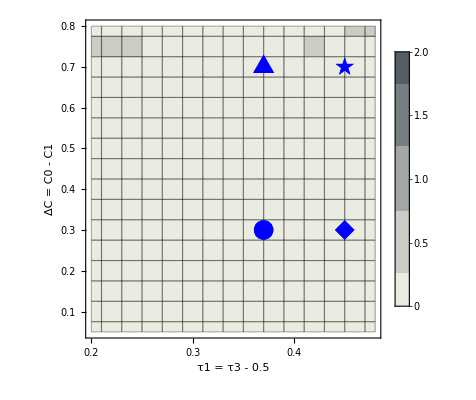

Fig4c_heatmap.png

```mathematica
(*Visualization*)
(*Draw the axes τ1 and τ3 with respect to the scale of the parameter δ*)
x1range={0.2,0.5};
x2range={0.7,1};
referencerange={0,0.3};
referenceticks=FindDivisions[Append[referencerange,0.05],7];
x1ticks=Quiet@Transpose@{referenceticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[referenceticks,referencerange,x1range]};
x2ticks=Quiet@Transpose@{referenceticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[referenceticks,referencerange,x2range]};

extract=simulation[[All,{1,2,3}]];
extract=extract.{{1,0,0},{0,1,0},{0,0,T/1000}};
g1= ListDensityPlot[extract,
Mesh->All,
InterpolationOrder->0,
PlotLegends->BarLegend[{Automatic,{0,2}}],
(*ColorFunction->(ColorData["DarkBands"][0.65*#/2]&),*)
ColorFunction->(ColorData["GrayTones"][1-0.6*Round[2*#]/4]&),
ColorFunctionScaling->False,
PlotLegends->Automatic,
(*FrameLabel->{{"C1",Automatic},{"τ1","τ3"}},*)
FrameLabel->{{"ΔC = C0 - C1",Automatic},{"τ1 = τ3 - 0.5",None}},
PlotRange->{Full,Full,{0,2}},
PlotRangeClipping->False,
LabelStyle->Directive[Black,FontSize->16],
(*FrameTicks->{{Automatic,Automatic},{x1ticks,x2ticks}}*)
FrameTicks->{{Automatic,Automatic},{x1ticks,Automatic}}
];
g2=ListPlot[pointList,
PlotMarkers->{
Style["▲",Blue,25],
Style["★",Blue,20],
Style["●",Blue,20],
Style["◆",Blue,20]}];
g3=Show[g1,g2]
Export[filename,g3]
```